## Diverging BH Entropy

Auxiliary notebook to the paper "Diverging black hole entropy from quantum infrared non-localities", by A. Platania & J. Redondo-Yuste.

### 0. Start

```mathematica
<<MaTeX`
```

```mathematica
colors = ColorData[10,"ColorList"] ;
```

### 1. Basic Formulas

The curvature invariants are Eqs. (18, 20):

```mathematica
RR=1/(2 r^2 ff[r]^2)(r^2 gg[r] ff'[r]^2-4 ff[r]^2(-1+gg[r]+r gg'[r])-r ff[r](r ff'[r]gg'[r]+2 gg[r](2 ff'[r]+r ff''[r])));
RR2=1/(2 r ff[r]^2)(r gg[r] ff'[r]^2-2 ff[r]^2 gg'[r]- ff[r](r ff'[r]gg'[r]+2 gg[r](2 ff'[r]+r ff''[r])));
RRtrtr=1/4(-ff'[r]^2/ff[r]+ff'[r]gg'[r]/gg[r]+2 ff''[r]);
```

With them, we compute the two auxiliary functions as in Eq. (23):

```mathematica
K1[x_]:=(RR-RR2)/.r->x//Simplify
K2[x_]:=(gg[r]/ff[r] RRtrtr+RR2/2//Simplify//Apart)/.r->x
```

Finally, we define the form of the metric functions:

```mathematica
f[r_] :=1-rs/r+Acoef/(r^n) ;
g[r_]:=1-rs/r+Acoef/(r^n) ;
```

Also, the location of the horizon is fixed by the coefficient A and the order n.

```mathematica
Solve[(Series[f[rs+ϵ], {ϵ,0,1}] // Normal) == 0, ϵ]
```

{{ϵ→(2 Acoef)/(-2^n+Acoef n)}}

```mathematica
ϵ[Acoef_, n_] := (Acoef rs)/(Acoef n -rs^n);
rh[Acoef_, n_] := rs + ϵ[Acoef, n];
```

### 2. Scaling with a (fixed value of α)

Now, let us try to compute everything analytically, for a given value of n.

```mathematica
n =30;
Acoef = ac rs^n/(n+1);
```

#### A) First term:

```mathematica
t1 = TimeUsed[];
ϕ[r_]:=K1[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ϕ[y],{y,x,Ry}, Assumptions->{rs>0 && Acoef >= 0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Series[%, {ac, 0, 1}] // Normal // Apart;
Integrate[%, x];
(% /. x-> Rx)- (% /. x-> r) // Simplify;
Term1Before = % /. Rx-> Ry // Simplify;
Series[% /. Rx-> Ry /. r-> rh[Acoef, n], {Ry, ∞, 0}] // Normal // Simplify;
Series[%, {ac,0,1}] // Normal;
Term1 = Series[%, {Ry, ∞,1},Assumptions->{rs>0, ac<1, ac>0} ] // Normal;
t2 = TimeUsed[]-t1;
StringForm["Time Elapsed: `` s" ,  NumberForm[t2,3]]
```

Time Elapsed: 13.2 s

#### B) Second term:

```mathematica
t1 = TimeUsed[];
ψ[r_]:=K2[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ψ[y],{y,x,Ry}, Assumptions->{rs>0 && Acoef >= 0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Series[%, {ac, 0, 1}] // Normal // Apart;
Integrate[%, x];
(% /. x-> Rx)- (% /. x-> r) // Simplify;
Term1Before = % /. Rx-> Ry // Simplify;
Series[% /. Rx-> Ry /. r-> rh[Acoef, n], {Ry, ∞, 0}] // Normal // Simplify;
Series[%, {ac,0,1}] // Normal;
Term2 = Series[%, {Ry, ∞,1},Assumptions->{rs>0, ac<1, ac>0} ] // Normal;
t2 = TimeUsed[]-t1;
StringForm["Time Elapsed: `` s" ,  NumberForm[t2,3]]
```

Time Elapsed: 10.8 s

#### C) Combine everything:

```mathematica
SW = 2Term1 - 4 Term2 // Simplify;
```

```mathematica
acoefs = {0.9,0.5,0.2,0.1,0.01, 0.001};
ntot = 6;
```

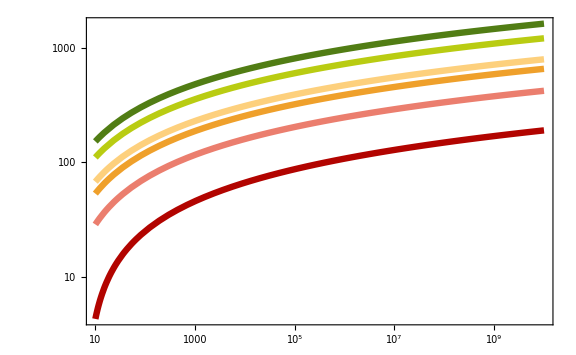

/Users/jaimeredondoyuste/Desktop/Convergence-A.pdf

```mathematica
fig=LogLogPlot[Evaluate@Table[(-Re[SW /. rs-> 1 /. ac-> acoefs[[ii]]]), {ii,1,ntot}],{Ry, 10, 10^(10)}, PlotStyle-> colors, Method->"DefaultPlotStyle"->Thickness[0.008], Frame-> True, FrameStyle-> Directive[FontSize-> 16], FrameLabel-> {MaTeX["R",Magnification-> 1.9], MaTeX["-\\Tilde{S}_W^{(1)}",Magnification-> 1.9]},ImageSize-> Large, PlotLegends-> Placed[LineLegend[ Evaluate@Table[Row@MaTeX[{"a = ",acoefs[[ii]]},Magnification->1.5],{ii,1,ntot}],LegendLayout-> {"Column",4}],{0.6,0.2}]]
Export["/Users/jaimeredondoyuste/Desktop/Convergence-A.pdf", fig]
```

### 3. Scaling with α

This needs to run Section 3 a few times, and after very run, execute the relevant command.

```mathematica
SW2 = SW /. rs-> 1 /. ac-> 0.1;
```

```mathematica
SW3 = SW/. rs-> 1 /. ac-> 0.1;
```

```mathematica
SW4 = SW/. rs-> 1 /. ac-> 0.1;
```

```mathematica
SW5 = SW/. rs-> 1 /. ac-> 0.1;
```

```mathematica
SW7 = SW/. rs-> 1 /. ac-> 0.1;
```

```mathematica
SW10 = SW/. rs-> 1 /. ac-> 0.1;
```

```mathematica
SW15 = SW/. rs-> 1 /. ac-> 0.1;
```

```mathematica
SW30 = SW/. rs-> 1 /. ac-> 0.1;
```

```mathematica
SWvals = {SW2, SW3, SW4, SW5, SW7, SW10, SW15, SW30};
ntot = 8;
ncoefs = {2,3,4,5,7,10,15,30};
```

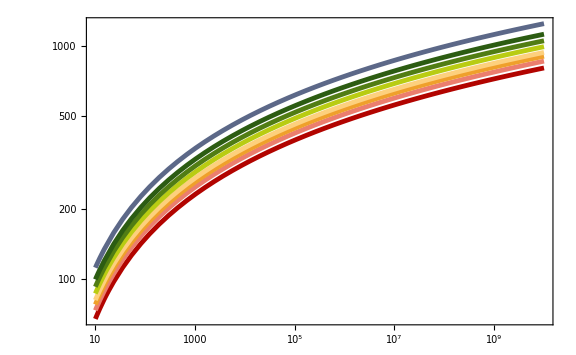

/Users/jaimeredondoyuste/Desktop/Convergence-n.pdf

```mathematica
fig = LogLogPlot[Evaluate@Table[-Re[SWvals[[ii]]], {ii,1,ntot}],{Ry,10,10^(10)}, PlotStyle-> colors,Method->"DefaultPlotStyle"->Thickness[0.006], Frame-> True, FrameStyle-> Directive[FontSize-> 16], FrameLabel-> {MaTeX["R",Magnification-> 1.9], MaTeX["-\\Tilde{S}_W^{(1)}",Magnification-> 1.9]},ImageSize-> Large, PlotLegends-> Placed[LineLegend[ Evaluate@Table[Row@MaTeX[{"\\alpha = ",ncoefs[[ii]]},Magnification->1.5],{ii,1,ntot}],LegendLayout-> {"Column",4}],{0.6,0.2}]]
Export["/Users/jaimeredondoyuste/Desktop/Convergence-n.pdf", fig]
```

### 4. Analytical formulas for α = 2 & Reissner-Nordström

The case for n=2 admits a simple solution, where we can see that the imaginary part is actually trivial, and therefore previously we were observing just a numerical artifact.

```mathematica
SW2 = SW;
```

```mathematica
Clear[n, Acoef]
```

```mathematica
n=2;
```

```mathematica
(*Acoef = ac rs^n/(n+1);*)
```

```mathematica
ϕ[r_]:=K1[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ϕ[y],{y,x,Ry}, Assumptions->{rs>0 && Acoef >= 0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Integrate[% , x];
(% /. x-> Rx)-(% /. x-> r)// Simplify
term1 = % /. r-> 1/2(rs + Sqrt[rs^2 - 4 Acoef]) ;
```

1/(√(-4 Acoef+rs^2))rs ((Log[(2 r-rs+√(-4 Acoef+rs^2))/(-rs+√(-4 Acoef+rs^2))]-Log[(-2 r+rs+√(-4 Acoef+rs^2))/(rs+√(-4 Acoef+rs^2))]) (Log[r]-Log[Ry])+(Log[(rs+√(-4 Acoef+rs^2)-2 Rx)/(rs+√(-4 Acoef+rs^2))]-Log[(-rs+√(-4 Acoef+rs^2)+2 Rx)/(-rs+√(-4 Acoef+rs^2))]) (Log[Rx]-Log[Ry])+PolyLog[2,(2 r)/(rs-√(-4 Acoef+rs^2))]-PolyLog[2,(2 r)/(rs+√(-4 Acoef+rs^2))]-PolyLog[2,(2 Rx)/(rs-√(-4 Acoef+rs^2))]+PolyLog[2,(2 Rx)/(rs+√(-4 Acoef+rs^2))])

```mathematica
ψ[r_]:=K2[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ψ[y],{y,x,Ry}, Assumptions->{rs>0 && Acoef >= 0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Integrate[% , x];
(% /. x-> Rx)-(% /. x-> r)// Simplify
term2 = % /. r-> rp // Simplify;
```

1/(2 Ry)3 ((2 rs Ry ArcTan[(-2 r+rs)/(√(4 Acoef-rs^2))])/(√(4 Acoef-rs^2))-(2 rs Ry ArcTan[(rs-2 Rx)/(√(4 Acoef-rs^2))])/(√(4 Acoef-rs^2))+2 Ry Log[r]-Ry Log[Acoef+r^2-r rs]-(rs Ry Log[r] Log[(2 r-rs+√(-4 Acoef+rs^2))/(-rs+√(-4 Acoef+rs^2))])/(√(-4 Acoef+rs^2))+(rs Ry Log[r] Log[(-2 r+rs+√(-4 Acoef+rs^2))/(rs+√(-4 Acoef+rs^2))])/(√(-4 Acoef+rs^2))-2 Ry Log[Rx]-(rs Ry Log[(rs+√(-4 Acoef+rs^2)-2 Rx)/(rs+√(-4 Acoef+rs^2))] Log[Rx])/(√(-4 Acoef+rs^2))+(rs Ry Log[Rx] Log[(-rs+√(-4 Acoef+rs^2)+2 Rx)/(-rs+√(-4 Acoef+rs^2))])/(√(-4 Acoef+rs^2))+Ry Log[Acoef-rs Rx+Rx^2]+(2 ArcTan[(-2 r+rs)/(√(4 Acoef-rs^2))] (2 Acoef-2 rs Ry+rs Ry Log[Ry]))/(√(4 Acoef-rs^2))-(2 ArcTan[(rs-2 Rx)/(√(4 Acoef-rs^2))] (2 Acoef-2 rs Ry+rs Ry Log[Ry]))/(√(4 Acoef-rs^2))-(rs Ry PolyLog[2,(2 r)/(rs-√(-4 Acoef+rs^2))])/(√(-4 Acoef+rs^2))+(rs Ry PolyLog[2,(2 r)/(rs+√(-4 Acoef+rs^2))])/(√(-4 Acoef+rs^2))+(rs Ry PolyLog[2,(2 Rx)/(rs-√(-4 Acoef+rs^2))])/(√(-4 Acoef+rs^2))-(rs Ry PolyLog[2,(2 Rx)/(rs+√(-4 Acoef+rs^2))])/(√(-4 Acoef+rs^2)))

The RN solution is obtained choosing A = Q. We can find the critical value of the coefficient such that the divergence changes sign as a function of the charge.

```mathematica
Acoef = ac rs^n/(n+1);
```

```mathematica
t1 = TimeUsed[];
ϕ[r_]:=K1[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ϕ[y],{y,x,Ry}, Assumptions->{rs>0 && Acoef >= 0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Series[%, {ac, 0, 1}] // Normal // Apart;
Integrate[%, x];
(% /. x-> Rx)- (% /. x-> r) // Simplify;
Term1Before = % /. Rx-> Ry // Simplify;
Series[% /. Rx-> Ry /. r-> rh[Acoef, n], {Ry, ∞, 0}] // Normal // Simplify;
Series[%, {ac,0,1}] // Normal;
Term1 = Series[%, {Ry, ∞,1},Assumptions->{rs>0, ac<1, ac>0} ] // Normal;
ψ[r_]:=K2[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ψ[y],{y,x,Ry}, Assumptions->{rs>0 && Acoef >= 0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Series[%, {ac, 0, 1}] // Normal // Apart;
Integrate[%, x];
(% /. x-> Rx)- (% /. x-> r) // Simplify;
Term1Before = % /. Rx-> Ry // Simplify;
Series[% /. Rx-> Ry /. r-> rh[Acoef, n], {Ry, ∞, 0}] // Normal // Simplify;
Series[%, {ac,0,1}] // Normal;
Term2 = Series[%, {Ry, ∞,1},Assumptions->{rs>0, ac<1, ac>0} ] // Normal;
t2 = TimeUsed[]-t1;
StringForm["Time Elapsed: `` s" ,  NumberForm[t2,3]] 
SWRN = 2Term1 - 4 coef Term2 /. ac-> 3 Q/rs^2 ;
```

Time Elapsed: 10.3 s

```mathematica
Qvals =Range[-0.41,0.39,(0.39-(-0.41))/100];
ntot = 100 + 1;
cvalsRN  =Table[{Qvals[[ii]], Re[coef /.  Flatten@Solve[Refine[ Re[(SWRN /. Q-> Qvals[[ii]]/. rs-> 1  /. Ry-> 10^(10))],Element[coef, Reals]]== 0, coef]]}, {ii,1,ntot}];
```

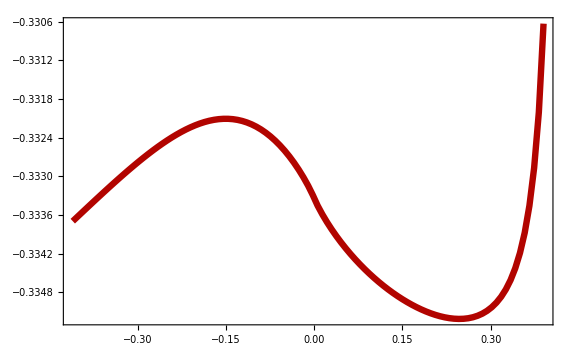

/Users/jaimeredondoyuste/Dropbox/Jaime-Ale - Non-local BH entropy/Figures/RN.pdf

```mathematica
fig = ListLinePlot[cvalsRN,PlotStyle->colors[[1]],Method->"DefaultPlotStyle"->Thickness[0.008], Frame-> True, FrameStyle-> Directive[FontSize-> 16], FrameLabel-> {MaTeX["Q / 2M ",Magnification-> 1.9], MaTeX["c_{crit}",Magnification-> 1.9]},ImageSize-> Large, PlotRange-> All, GridLines->None, PlotTheme-> "Scientific"]
Export["/Users/jaimeredondoyuste/Dropbox/Jaime-Ale - Non-local BH entropy/Figures/RN.pdf", fig]
```

### 5. Dependence on the Coefficients

Let us look now carefully at how does our result depend on the sign of the coefficients. First, we restrict our attention to the Schwarzschild case.

#### A) Schwarzschild case:

```mathematica
n=1;
Acoef = ac rs^n/(n+1);
ac = 0
```

0

```mathematica
t1 = TimeUsed[];
ϕ[r_]:=K1[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ϕ[y],{y,x,Ry}, Assumptions->{rs>0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Integrate[%, x];
(% /. x-> Rx)- (% /. x-> r) // Simplify;
Term1 = % /. Rx-> Ry // Simplify;
t2 = TimeUsed[]-t1;
StringForm["Time Elapsed: `` s" ,  NumberForm[t2,3]]
```

Time Elapsed: 2.1 s

```mathematica
t1 = TimeUsed[];
ψ[r_]:=K2[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ψ[y],{y,x,Ry}, Assumptions->{rs>0 && Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Integrate[%, x];
(% /. x-> Rx)- (% /. x-> r) // Simplify;
Term2 = % /. Rx-> Ry // Simplify;
t2 = TimeUsed[]-t1;
StringForm["Time Elapsed: `` s" ,  NumberForm[t2,3]]
```

Time Elapsed: 1.36 s

Now fix c_{1,1} = 1. What matters is the relative sign, of course.

```mathematica
SW = 2 Term1 - 4 coef Term2 // Simplify;
```

```mathematica
SW  /. r-> rh[Acoef, n] /. rs-> 1
```

(1+3 coef) (-π^2/3+-∞ Log[Ry]+2 PolyLog[2,Ry])

The critical value is achieved when c_{1,3} = -1/3c_{1,1}.

```mathematica
SW /. rs-> 1 /. coef-> -1/3 // Simplify
```

0

#### B) Generalized version:

Choose parameters.

```mathematica
Clear[n, Acoef, ac]
```

```mathematica
n=30;
Acoef =ac rs^n/(n+1);
```

The calculation itself.

```mathematica
t1 = TimeUsed[];
ϕ[r_]:=K1[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ϕ[y],{y,x,Ry}, Assumptions->{rs>0 && Acoef >= 0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Series[%, {ac, 0, 1}] // Normal // Apart;
Integrate[%, x];
(% /. x-> Rx)- (% /. x-> r) // Simplify;
Term1Before = % /. Rx-> Ry // Simplify;
Series[% /. Rx-> Ry /. r-> rh[Acoef, n], {Ry, ∞, 0}] // Normal // Simplify;
Series[%, {ac,0,1}] // Normal;
Term1 = Series[%, {Ry, ∞,1},Assumptions->{rs>0, ac<1, ac>0} ] // Normal;
t2 = TimeUsed[]-t1;
StringForm["Time Elapsed: `` s" ,  NumberForm[t2,3]]
```

Time Elapsed: 45.2 s

```mathematica
t1 = TimeUsed[];
ψ[r_]:=K2[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ψ[y],{y,x,Ry}, Assumptions->{rs>0 && Acoef >= 0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Series[%, {ac, 0, 1}] // Normal // Apart;
Integrate[%, x];
(% /. x-> Rx)- (% /. x-> r) // Simplify;
Term1Before = % /. Rx-> Ry // Simplify;
Series[% /. Rx-> Ry /. r-> rh[Acoef, n], {Ry, ∞, 0}] // Normal // Simplify;
Series[%, {ac,0,1}] // Normal;
Term2 = Series[%, {Ry, ∞,1},Assumptions->{rs>0, ac<1, ac>0} ] // Normal;
t2 = TimeUsed[]-t1;
StringForm["Time Elapsed: `` s" ,  NumberForm[t2,3]]
```

Time Elapsed: 40.7 s

```mathematica
SW = 2Term1 - 4 coef Term2 // Simplify;
```

#### C) Some plots:

```mathematica
Solve[Refine[ Re[(SW /. ac->3/4/. rs-> 1  /. Ry-> 10^(20))],Element[coef, Reals]]== 0, coef]  // N;
coefvals = {  -1, Re[coef/. Flatten@ %], 1};
ntot = 3;
pstyle = Table[{colors[[ii]], Magnification[3]}, {ii,1,ntot}];
```

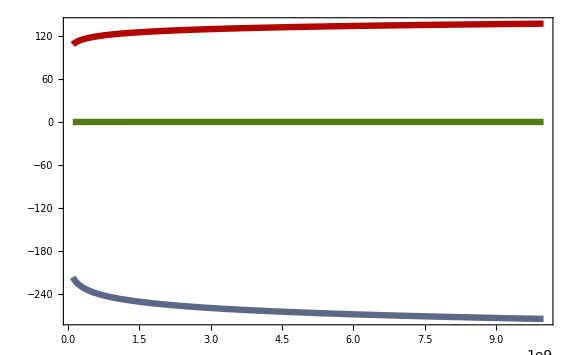

/Users/jaimeredondoyuste/Dropbox/Jaime-Ale - Non-local BH entropy/Figures/RN.pdf

```mathematica
fig = Plot[Evaluate@Table[Re[SW /. ac-> 3/4 /. rs-> 1 /. coef-> coefvals[[ii]]],{ii,1,ntot}],{Ry, 10^8, 10^10},PlotStyle->{colors[[1]], colors[[6]], colors[[8]]},Method->"DefaultPlotStyle"->Thickness[0.008], Frame-> True, FrameStyle-> Directive[FontSize-> 16], FrameLabel-> {MaTeX["R",Magnification-> 1.9], MaTeX["\Delta S_W",Magnification-> 1.9]},ImageSize-> Large, PlotLegends-> Placed[LineLegend[Evaluate@Table[Row@MaTeX[{" \\frac{c_{1,3}}{c_{1,1}}= ",NumberForm[coefvals[[ii]],3]},Magnification->1.3],{ii,1,ntot}],LegendLayout-> {"Column",4}],{0.6,0.3}], PlotRange-> All]
Export["/Users/jaimeredondoyuste/Dropbox/Jaime-Ale - Non-local BH entropy/Figures/RN.pdf", fig]
```

I want to check how does the critical value change when computed at different values of Ry.

```mathematica
Ryvals = 10.0^Range[1, 12, (12-1)/100];
ntot = 101;
cvals = Table[{Ryvals[[ii]], -Re[coef /.  Flatten@Solve[(SW /. ac-> 0.1 /. rs-> 1  /. Ry-> Ryvals[[ii]])== 0, coef]]}, {ii,1,ntot}];
```

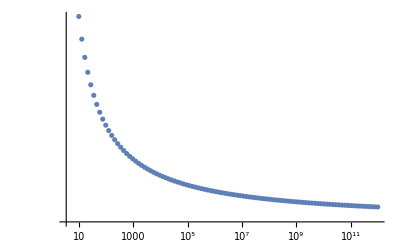

```mathematica
ListLogLogPlot[cvals, PlotRange->All]
```

It seems that it converges at very high values of R_y. What is that function, though?

```mathematica
acvals =10.0^Range[-6,0,0-(-6)/100];
ntot = 100 + 1;
cvals  =Table[{acvals[[ii]], Re[coef /.  Flatten@Solve[(SW /. ac-> acvals[[ii]] /. rs-> 1  /. Ry-> 10^10)== 0, coef]]}, {ii,1,ntot}];
```

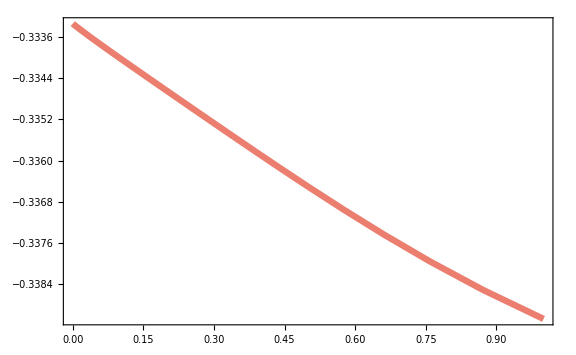

```mathematica
ListLinePlot[cvals,PlotStyle->colors[[2]],Method->"DefaultPlotStyle"->Thickness[0.008], Frame-> True, FrameStyle-> Directive[FontSize-> 16], FrameLabel-> {MaTeX["A_c",Magnification-> 1.9], MaTeX["c_{crit}",Magnification-> 1.9]},ImageSize-> Large, PlotRange-> All]
```

#### D): Scaling of c_{crit} with A_c and with n.

Run the previous code several times to produce the following values.

```mathematica
SW2 = SW;
```

```mathematica
SW3 = SW;
```

```mathematica
SW4 = SW;
```

```mathematica
SW5 = SW;
```

```mathematica
SW7 = SW;
```

```mathematica
SW10 = SW;
```

```mathematica
SW15 = SW;
```

```mathematica
SW30 = SW;
```

```mathematica
acvals =10.0^Range[-3,-0.2,(-0.2-(-3))/100];
nvals = {2,3,4,5,7,10,15,30};
ntotv = 8;
ntot = 100 + 1;
cvals2  =Table[{Log[acvals[[ii]]],Log[- Re[coef /.  Flatten@Solve[Refine[ Re[(SW2 /. ac-> acvals[[ii]]/. rs-> 1  /. Ry-> 10^(10))],Element[coef, Reals]]== 0, coef]]]}, {ii,1,ntot}];
cvals3  =Table[{Log[acvals[[ii]]],Log[ -Re[coef /.  Flatten@Solve[Refine[ Re[(SW3 /. ac-> acvals[[ii]] /. rs-> 1  /. Ry-> 10^(10))],Element[coef, Reals]]== 0, coef]]]}, {ii,1,ntot}];
cvals4  =Table[{Log[acvals[[ii]]],Log[ -Re[coef /.  Flatten@Solve[Refine[ Re[(SW4 /. ac-> acvals[[ii]] /. rs-> 1  /. Ry-> 10^(10))],Element[coef, Reals]]== 0, coef]]]}, {ii,1,ntot}];
cvals5  =Table[{Log[acvals[[ii]]],Log[- Re[coef /.  Flatten@Solve[Refine[ Re[(SW5 /.ac-> acvals[[ii]] /. rs-> 1  /. Ry-> 10^(10))],Element[coef, Reals]]== 0, coef]]]}, {ii,1,ntot}];
cvals7  =Table[{Log[acvals[[ii]]],Log[ -Re[coef /.  Flatten@Solve[Refine[ Re[(SW7 /. ac-> acvals[[ii]]/. rs-> 1  /. Ry-> 10^(10))],Element[coef, Reals]]== 0, coef]]]}, {ii,1,ntot}];
cvals10  =Table[{Log[acvals[[ii]]],Log[ -Re[coef /.  Flatten@Solve[Refine[ Re[(SW10 /. ac-> acvals[[ii]] /. rs-> 1  /. Ry-> 10^(10))],Element[coef, Reals]]== 0, coef]]]}, {ii,1,ntot}];
cvals15  =Table[{Log[acvals[[ii]]],Log[ -Re[coef /.  Flatten@Solve[Refine[ Re[(SW15 /. ac-> acvals[[ii]] /. rs-> 1  /. Ry-> 10^(10))],Element[coef, Reals]]== 0, coef]]]}, {ii,1,ntot}];
cvals30  =Table[{Log[acvals[[ii]]],Log[ -Re[coef /.  Flatten@Solve[Refine[ Re[(SW30 /. ac-> acvals[[ii]] /. rs-> 1  /. Ry-> 10^(10))],Element[coef, Reals]]== 0, coef]]]}, {ii,1,ntot}];
```

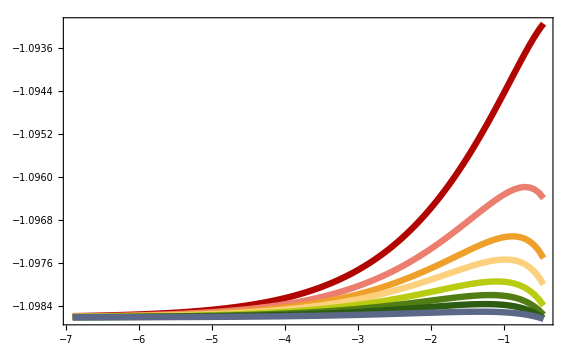

/Users/jaimeredondoyuste/Dropbox/Jaime-Ale - Non-local BH entropy/Figures/Fixed-point.pdf

```mathematica
fig = ListLinePlot[{cvals2, cvals3,cvals4, cvals5, cvals7, cvals10, cvals15,cvals30},PlotStyle->colors,Method->"DefaultPlotStyle"->Thickness[0.008], Frame-> True, FrameStyle-> Directive[FontSize-> 16], FrameLabel-> {MaTeX["\\log(a)",Magnification-> 1.9], MaTeX["\\log \\, (-c_{crit})",Magnification-> 1.9]},ImageSize-> Large, PlotRange-> All,PlotLegends-> Placed[LineLegend[Evaluate@Table[Row@MaTeX[{" \\alpha= ",nvals[[ii]]},Magnification->1.3],{ii,1,ntotv}],LegendLayout-> {"Column",4}],{0.35,0.5}]]
Export["/Users/jaimeredondoyuste/Dropbox/Jaime-Ale - Non-local BH entropy/Figures/Fixed-point.pdf", fig]
```

### 6. Limit as r -> r_H

```mathematica
n =2;
Acoef = ac rs^n/(n+1);
Rx = Ry = 10^3;
```

```mathematica
t1 = TimeUsed[];
ϕ[r_]:=K1[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ϕ[y],{y,x,Ry}, Assumptions->{rs>0 && ac >= 0 &&Re[x]≥0&&x∈Reals&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Integrate[%, x];
Term1=(% /. x-> Rx)- (% /. x-> r) // Simplify;
t2 = TimeUsed[]-t1;
StringForm["Time Elapsed: `` s" ,  NumberForm[t2,3]]
```

Time Elapsed: 18.1 s

```mathematica
t1 = TimeUsed[];
ψ[r_]:=K2[r]/.{gg->Function[x,g[x]],ff->Function[x,f[x]]}//Simplify;
Integrate[(f[y]/g[y])^(1/2)y^2 ψ[y],{y,x,Ry}, Assumptions->{rs>0 && ac >= 0 , Re[Ry]≥0&&Re[x]≥0&&Ry∈Reals&&x∈Reals&&Ry>0&&Ry≠x&&x>=0 }];
Evaluate[-x^-2(f[x]g[x])^(-1/2)%//PowerExpand] // Simplify;
Integrate[%, x];
Term2=(% /. x-> Rx)- (% /. x-> r) // Simplify;
t2 = TimeUsed[]-t1;
StringForm["Time Elapsed: `` s" ,  NumberForm[t2,3]]
```

Time Elapsed: 1.36 s

```mathematica
SW = 2Term1 - 4 Term2 // Simplify;
```

```mathematica
acoefs = {0.6,0.5,0.2,0.1,0.01, 0.001};
ntot = 6;
```

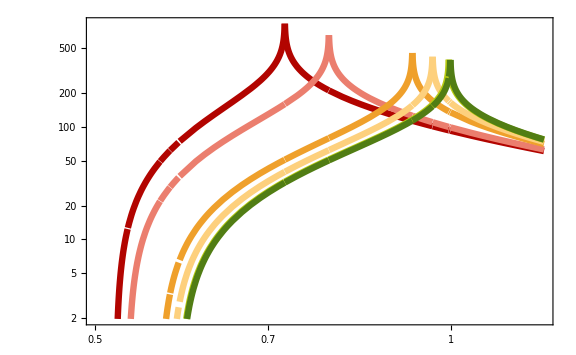

/Users/jaimeredondoyuste/Desktop/Divergence_rS.pdf

```mathematica
fig=LogLogPlot[Evaluate@Table[(-Re[SW /. r-> x rs /. rs-> 2 /. ac-> acoefs[[ii]]]), {ii,1,ntot}],{x, 0.5,1.2}, PlotStyle-> colors, Method->"DefaultPlotStyle"->Thickness[0.008], Frame-> True, FrameStyle-> Directive[FontSize-> 16], FrameLabel-> {MaTeX["r/r_s",Magnification-> 1.9], MaTeX["-\\Tilde{S}_W^{(1)}",Magnification-> 1.9]},ImageSize-> Large, PlotLegends-> Placed[LineLegend[ Evaluate@Table[Row@MaTeX[{"a = ",acoefs[[ii]]},Magnification->1.5],{ii,1,ntot}],LegendLayout-> {"Column",4}],{0.67,0.2}]]
Export["/Users/jaimeredondoyuste/Desktop/Divergence_rS.pdf", fig]
```